```mathematica
1+1
```

2

```mathematica
nestedSine[n_, x_]:=Module[{sine=Sin[x], sign=1, s=2*Sin[x]},Table[sign*=-1;s+=sign*sine;sine=Sin[sine];,{i, 2, n+1}];s]
```

```mathematica
nestedNSine[n_, x_]:=nestedSine[n, nestedSine[n, x]]/1.5
nestedNSine[n_][x_]:=nestedNSine[n, x]
```

```mathematica
error[func_]:=NIntegrate[(Sin[x]-func[x])^2, {x, -2Pi, 2Pi}]
```

```mathematica
Plot[{Sin[x],nestedNSine[501, x]}, {x, -7, 7}]
```

$Aborted

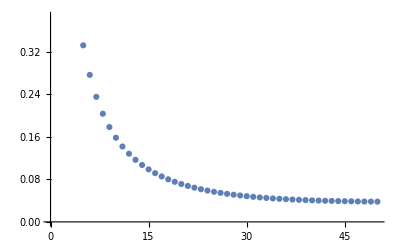

```mathematica
als=ParallelMap[error[nestedNSine[#]]&,Range[1,100,2]];
ListPlot[als]
```

```mathematica
eals=Table[als[[i]], {i, 1, Length[als], 2}];
```

NIntegrate::inumr: The integrand (Sin[x]-(0.666667 series[1])[x])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-6.28319,6.28319}}.

NIntegrate::inumr: The integrand (Sin[x]-(0.666667 series[2])[x])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-6.28319,6.28319}}.

NIntegrate::inumr: The integrand (Sin[x]-(0.666667 series[3])[x])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-6.28319,6.28319}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
oals=Table[als[[i+1]], {i, 1, Length[als], 2}];
```

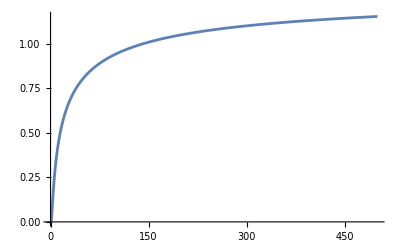

```mathematica
ListLinePlot[eals]
```

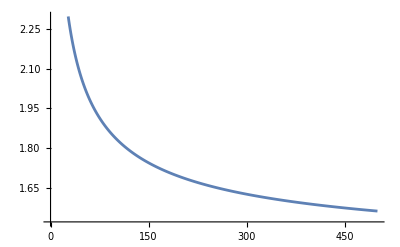

```mathematica
ListLinePlot[oals]
```

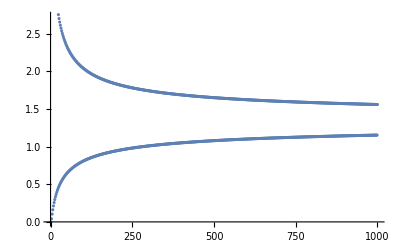

```mathematica
ListPlot[als]
```

```mathematica
series[1][x]
```

Sin[x]

```mathematica
series2[n_]:=Sin[x]+Sum[((-1)^(i+1))*Nest[Sin,x,i+1],{i,n}]
```

```mathematica
series2[1]
```

Sin[x]+Sin[Sin[x]]

```mathematica
series[2][x]
series2[2]
```

Sin[x]+Sin[Sin[x]]

Sin[x]+Sin[Sin[x]]-Sin[Sin[Sin[x]]]

```mathematica
s50=series[50][x];
r1[x_]:=s50
r[x_]:=series2[51]
```

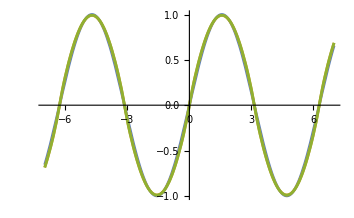

```mathematica
Plot[{Sin[x], r[r[x]]/1.58, r1[r1[x]]/1.58}, {x, -7,7}]
```

```mathematica
n50=s50/.(x->s50);
```

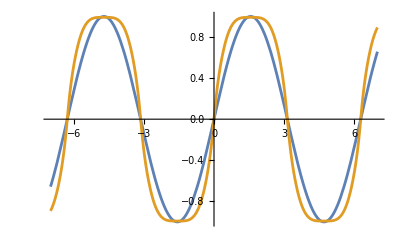

```mathematica
Plot[{Sin[x], n50/1.58}, {x, -7, 7}]
```

```mathematica
r=series2[501];
```

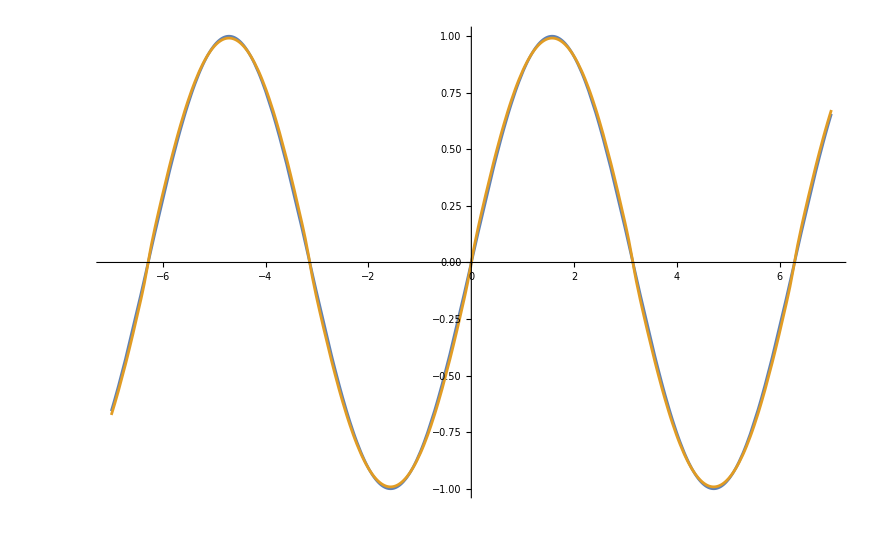

```mathematica
Plot[{Sin[x], (r/.(x->r))/1.5}, {x, -7, 7}]
```

```mathematica
series[n_]:=2 Sin[x]+(#.Drop[NestList[Sin,x,Length[#]],1]&@Table[(-1)^i,{i,n}])
```

```mathematica
series[3]
```

Sin[x]+Sin[Sin[x]]-Sin[Sin[Sin[x]]]

```mathematica
{Sin[1], Sin[Sin[1]], Sin[Sin[Sin[1]]]}//N
```

{0.841471,0.745624,0.67843}

```mathematica
series[3]/.x->1.
```

0.908665

```mathematica
series[1000]/.x->1.
```

1.26089

```mathematica
AbsoluteTiming[series[1000]/.x->1.]
```

{0.195995,1.26089}

```mathematica
(7206600/1000000000)//N
```

0.0072066

```mathematica
0.195995/0.0072066
```

27.1966

```mathematica
r=series[11];
```

```mathematica
r15=(r/.(x->r))/1.5;
```

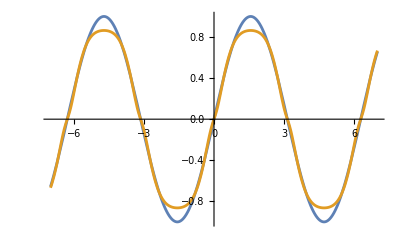

```mathematica
Plot[{Sin[x], r15}, {x, -7,7}]
```

```mathematica
progressMap[func_,l_List, message_:"Complete"]:=Module[
{originalTime=AbsoluteTime[],progress=PrintTemporary["0% "<>message], timeUsed},
timeUsed:=AbsoluteTime[]-originalTime;
Table[NotebookDelete[progress];
progress=PrintTemporary[ToString[Round[100*i/Length[l]]]<>"% "<>message<>" (ETA: "<>DateString[AbsoluteTime[]+Round[(timeUsed/i)*(Length[l]-i)]]<>")"];
func[l[[i]]],{i, Length[l]}]]
```

```mathematica
(Plus@@ParallelMap[(Sin[#]-(r15/.(x->#)))^2&,Subdivide[-2Pi, 2Pi, 4^#]])&/@Range[1,8]
```

$Aborted

```mathematica
(Plus@@ParallelMap[(Sin[#]-(r15/.(x->#)))^2&,Subdivide[-2Pi, 2Pi,10]])/10
```

0.0216406

```mathematica
r15/.x->1.
```

0.682804

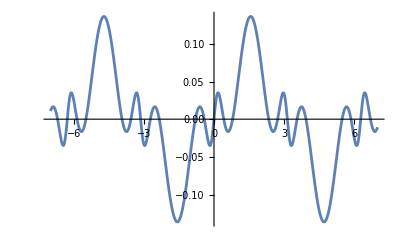

```mathematica
Plot[Sin[x]-r15, {x, -7,7}]
```